# Name:

Show an appropriate amount of work.  You can (and probably should) check your work with a computer.

Compute the magnitude and argument or real and imaginary parts for all possible values of

z=(ⅈ/(1+ⅈ))^3              
 abs(z)=                                             
 arg(z)=

The roots of z^5=-243 ⅈ     
 abs(z)=                                               
 arg(z)=

The roots of (z-ⅈ)(z^2-4 ⅈ z+5)=0     
 re(z)=                                                  
 im(z)=

Sketch and label the sets

Sketch the set of points C_1 that satisfy |z+ⅈ|<2.

Sketch the set of points C_2 that satisfy re(z-ⅈ)=1.

Sketch the set of points C_3 that satisfy arg(z+ⅈ)=3π/4.

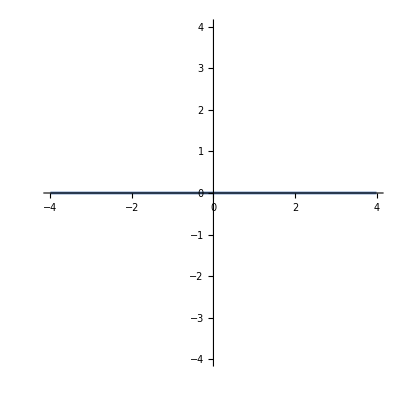

For f(z)=u(x,y)+ⅈ v(x,y) and write down the CR equations
                                             and

For cos(z) complete the following
u(x,y)=                                             and v(x,y)=                                            
∂_x u=                                             and ∂_x v=                                            
∂_y u=                                             and ∂_y v=                                            
Analytic Yes or No

For ⅈ x^2-2 x y-ⅈ y^2 complete the following
u(x,y)=                                             and v(x,y)=                                            
∂_x u=                                             and ∂_x v=                                            
∂_y u=                                             and ∂_y v=                                            
Analytic Yes or No                                              .  
If yes f(z)=

For ⅈ x^2-2 x y- y^2 complete the following
u(x,y)=                                             and v(x,y)=                                            
∂_x u=                                             and ∂_x v=                                            
∂_y u=                                             and ∂_y v=                                            
Analytic Yes or No                                              .  
If yes f(z)=

Is ⅇ^(x-ⅈ y) analytic? Yes or No                                              .  Show your work below.

Explain why the real part u of an analytic function satisfies u_xx+u_yy=0.

Compute ∫_O ⅇ^(1/z) dz for the ccw unit circle. #5.6.1 p166

Show ∫_0^∞ dx/(x^4+2 x^2 cos(2α)+1)=|π/(4 cos(α))| 	#5.6.4 p166

Show ∫_0^∞ (ⅇ^-x-cos(x) dx)/x=0  			#5.6.5 p166

Show ∫_(-∞)^∞ dx/(1+x^(2p))=|π/(p sin(π/(2p)))| 		#5.6.7 p166

Compute ∫_(-∞)^∞ z/(z^3+ⅈ)dz by computing lim_(R->∞) ∫_Γ_R z/(z^3+ⅈ)dz where Γ_R is the ccw semi-circle contour shown below for R=3.  Explain your steps and show appropriate work.

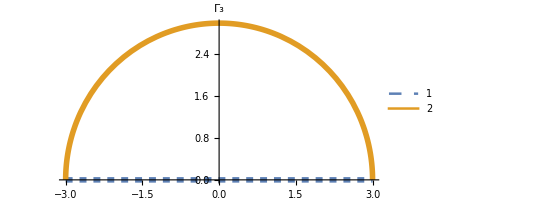

```mathematica
p1[R_][t_]:=R(-1+2 t)
p2[R_][t_]:=R ⅇ^(ⅈ π t)
f[z_]:=z/(z^3+ⅈ)
ReIm[FunctionPoles[f[z],z]];
R=3; ParametricPlot[{ReIm[p1[R][t]],ReIm[p2[R][t]]},{t, 0, 1},
PlotStyle->{{Dashed,Thickness[0.01]},{Thickness[0.01]},{DotDashed,Thickness[0.01]}},
PlotLegends->Automatic,PlotLabel->"Γ_3"]
```

Compute ∫_(-∞)^∞ z/(z^2+4)dz by computing lim_(R->∞) ∫_Γ_R z/(z^3+ⅈ)dz where Γ_R is the ccw semi-circle contour shown below for R=3.  Explain your steps and show appropriate work.

```mathematica
p1[R_][t_]:=R(-1+2 t)
p2[R_][t_]:=R ⅇ^(ⅈ π t)
f[z_]:=z/(z^2+4)
ReIm[FunctionPoles[f[z],z]];
R=3; ParametricPlot[{ReIm[p1[R][t]],ReIm[p2[R][t]]},{t, 0, 1},
PlotStyle->{{Dashed,Thickness[0.01]},{Thickness[0.01]},{DotDashed,Thickness[0.01]}},
PlotLegends->Automatic,PlotLabel->"Γ_3"]
```

-Graphics-

You may not remember from Calculus but the derivative of arcsin(z) is 1/√(1-z^2).

Discuss the singularities of arcsin(z) for z∈ℂ

Work out the first few terms of the Taylor Series for arcsin(z) about z=0.

What is the radius of convergence for the TS about z=0?

What would be the radius of convergence for the TS about z=ⅈ?

You may not remember from Calculus but the derivative of arctan(z/a) is a/(a^2+z^2).

Discuss the singularities of arctan(z) for z∈ℂ

Work out the first few terms of the Taylor Series for arctan(z) about z=0.

What is the radius of convergence for the TS about z=0?

What would be the radius of convergence for the TS about z=2?

The Laurent Series for a function f(z)=∑_(n=-∞)^(n=∞) a_n z^n

What is the name for a_-1?  Why is it particularly important?

Give a simple formulas for a_n with n≥0 valid when f is analytic near z=0.

Give a formulas for a_n valid even when f is not analytic near z=0.  Explain when this formula is valid.

Explain why we can write ⅇ^(z+1/z)=∑_(n=-∞)^(n=∞) a_n z^n.  Write down an integral for a_n.

Compute lim_(n→∞) ∑_(k=-n)^(k=n) 1/(n^4+1)using a contour integral. Explain your steps and show appropriate work.  In this problem you do not need to compute residues. If you have defined f and z_i you can just write res(f,z_i) for the residue.

For the closed counter clockwise contour Γ shown below 
p_1(t)=                                                              for 0≤t<1
p_2(t)=                                                              for 0≤t<1
∫_Γ f(z)dz=∫_0^1                                           dt+∫_0^1                                           dt.
For f(z)=z^2/(z-ⅈ) evaluate ∫_Γ f(z)dz=                                              .  Show appropriate work below.

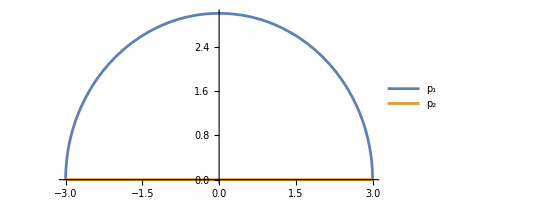

```mathematica
p1[t_]:=3 E^(π ⅈ t)
p2[t_]:=-3+6 t
ParametricPlot[{ReIm[p1[t]],ReIm[p2[t]]},{t,0,1},PlotLegends->{"p_1","p_2"}]
```

For the closed counter clockwise contour Γ shown below

p_1(t)=                                                              for 0≤t<1
p_2(t)=                                                              for 0≤t<1
p_3(t)=                                                              for 0≤t<1 
∫_Γ f(z)dz=∫_0^1                                           dt+∫_0^1                                           dt+∫_0^1                                           dt
For f(z)=ⅈ/(z-(1+2ⅈ)) evaluate ∫_Γ f(z)dz=                                                  .

Explain briefly the need for care if you evaluate the individual line integrals using the fundamental theorem of calculus and logs.

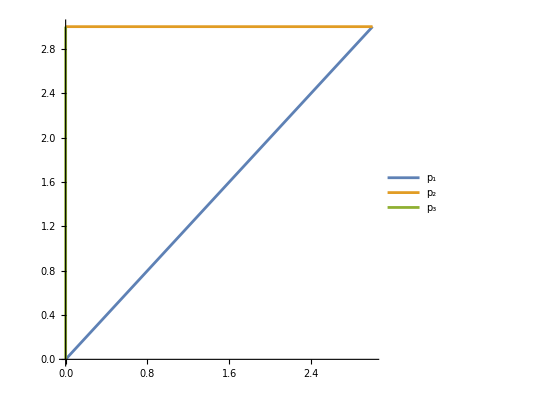

```mathematica
p1[t_]:=(3+3 ⅈ)t
p2[t_]:=3+3ⅈ -3 t
p3[t_]:= 3 ⅈ - 3 ⅈ t
ParametricPlot[{ReIm[p1[t]],ReIm[p2[t]],ReIm[p3[t]]},{t,0,1},PlotLegends->{"p_1","p_2","p_3"}]
```

Compute ∫_Γ ⅇ^z/((z^2+9)(z-3))dz=                                                             for the counter clockwise contour Γ. Show appropriate work.

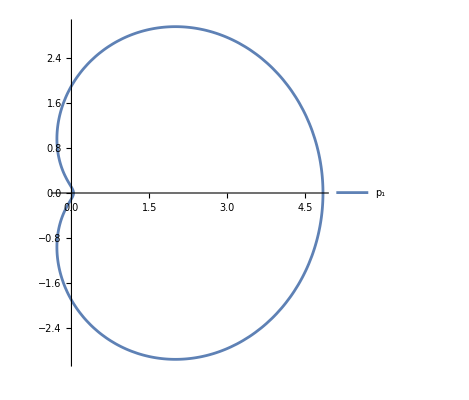

```mathematica
p1[t_]:=(E^(2π ⅈ t)+1.2)^2
ParametricPlot[ReIm[p1[t]],{t,0,1},PlotLegends->{"Γ"}]
```